```mathematica
raw=OpenRead["G:\\CSCI 561 AI\\HW3\\reviews.csv"];
```

```mathematica
reviews=Map[StringSplit[#,"|"]&,ReadList[raw,String]];
```

```mathematica
positiveReviews=Select[reviews,#[[1]]=="positive"&];
```

```mathematica
negativeReviews=Select[reviews,#[[1]]=="negative"&];
```

```mathematica
randomPositiveReviews=RandomSample[positiveReviews];
```

```mathematica
randomNegativeReviews=RandomSample[negativeReviews];
```

```mathematica
positiveTrainingSet=randomPositiveReviews[[1;;5000,All]];
```

```mathematica
negativeTrainingSet=randomNegativeReviews[[1;;5000,All]];
```

```mathematica
positiveTrainingReview=positiveTrainingSet[[1;;5000,2]];
```

```mathematica
negativeTrainingReview=negativeTrainingSet[[1;;5000,2]];
```

```mathematica
prePositive=List[];
```

```mathematica
Do[PrependTo[prePositive,StringDelete[ToLowerCase[DeleteStopwords[positiveTrainingReview[[i]]]],RegularExpression["[\\.\"\',\!]"]]],{i,1,Length@positiveTrainingReview}];
```

```mathematica
prePositive
```

{subtle message: wow-    little nervous  read  book    130 pages    unassuming reading 1984  hs   dubious  enjoying   george orwells    grown        easier   interesting/intelligable read  way  enjoyed animal farm! parts   help  laugh   subtle irony  parts got  thinking   deeper level      book   curious   story  going    end    point  ( chose  read  foreward        spoilers) think    great subtle novel        required reading  school    reasons  enjoyed       easy straight forward read! gets  thinking   good thing!,4998,   best book  mario puzo:   awestruck   finish  book    complete like none    work great book   great author}
 |  |  |  |

```mathematica
prePositive=WordStem[prePositive];
```

```mathematica
preNegative=List[];
```

```mathematica
Do[PrependTo[preNegative,StringDelete[ToLowerCase[DeleteStopwords[negativeTrainingReview[[i]]]],RegularExpression["[\\.\"\',\!]"]]],{i,1,Length@negativeTrainingReview}];
```

```mathematica
preNegative=WordStem[preNegative]
```

{wrong dvd:  ordered  vol 3  vol 4   accelerracers  packaging    case  disk  vol 3 said   breaking point  actual movie  ultimate race   vol 4  son   let  know     past time  return  product     stuck  2 copies  vol 4check  copy   receive   make sure    correct volum,4998, star:  feel   plastic  somewhat soft   silky  steel grommets fell   length    described  edges   bit rag}
 |  |  |  |

```mathematica
fePositive=FeatureExtraction[prePositive,"TFIDF"];
```

```mathematica
feNegative=FeatureExtraction[preNegative,"TFIDF"];
```

```mathematica
trainingSet=Join[prePositive,preNegative];
```

```mathematica
trainingSet
```

{subtle message: wow-    little nervous  read  book    130 pages    unassuming reading 1984  hs   dubious  enjoying   george orwells    grown        easier   interesting/intelligable read  way  enjoyed animal farm! parts   help  laugh   subtle irony  parts got  thinking   deeper level      book   curious   story  going    end    point  ( chose  read  foreward        spoilers) think    great subtle novel        required reading  school    reasons  enjoyed       easy straight forward read! gets  thinking   good thing!,9998, star:  feel   plastic  somewhat soft   silky  steel grommets fell   length    described  edges   bit rag}
 |  |  |  |

```mathematica
featureSet=FeatureExtraction[trainingSet,"TFIDF"];
```

```mathematica
featureSetValues=featureSet[trainingSet];
```

```mathematica
dr=DimensionReduce[featureSetValues,100];
```

```mathematica
Dimensions[dr]
```

{10000,100}
 |  |  |  |

```mathematica
toAppendList=Classify["Sentiment",trainingSet,"Probabilities"];
valuesAppend=Values[toAppendList];
```

```mathematica
newFeatureSet = List[];
```

```mathematica
Do[PrependTo[newFeatureSet, Join[dr[[i]],valuesAppend[[i]]]],{i,1,Length@valuesAppend}];
```

```mathematica
Dimensions[newFeatureSet]
```

{10000,103}
 |  |  |  |

```mathematica
positiveDr2=newFeatureSet[[1;;4000,All]];
```

```mathematica
negativeDr2=newFeatureSet[[5001;;9000,All]];
```

```mathematica
trainingDr2=Join[positiveDr2,negativeDr2];
```

```mathematica
positiveDrT2=newFeatureSet[[4001;;5000,All]];
```

```mathematica
negativeDrT2=newFeatureSet[[9001;;10000,All]];
```

```mathematica
testingDr2=Join[positiveDrT2,negativeDrT2];
```

```mathematica
positiveLabel=randomPositiveReviews[[1;;4000,1]];
```

```mathematica
negativeLabel=randomNegativeReviews[[1;;4000,1]];
```

```mathematica
labelReviewTraining=Join[positiveLabel,negativeLabel];
```

```mathematica
positivelevelT=randomPositiveReviews[[1;;1000,1]];
```

```mathematica
negativelevelT=randomNegativeReviews[[1;;1000,1]];
```

```mathematica
labelTraining=Join[positivelevelT,negativelevelT];
```

```mathematica
sentimentAnalysisRF=Classify[trainingDr2->labelReviewTraining,Method->"RandomForest"];
```

```mathematica
cmRF=ClassifierMeasurements[sentimentAnalysisRF,testingDr2->labelTraining];
```

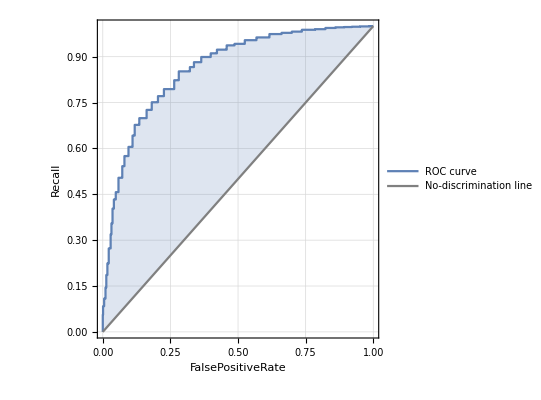
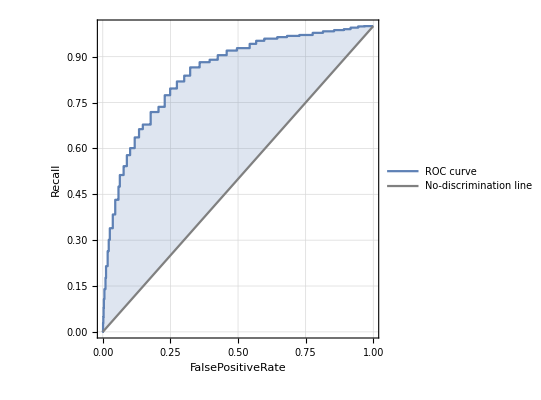
0.765
<|negative→0.750473,positive→0.781316|>
<|negative→0.794,positive→0.736|>
<|negative→-Graphics-,positive→-Graphics-|>
 |  |  |  |

```mathematica
cmRF/@{"Accuracy","Precision","Recall", "ROCCurve"}//TableForm
```

```mathematica
sentimentAnalysisNN=Classify[trainingDr2->labelReviewTraining,Method->"NeuralNetwork"];
```

```mathematica
cmNN=ClassifierMeasurements[sentimentAnalysisNN,testingDr2->labelTraining];
```

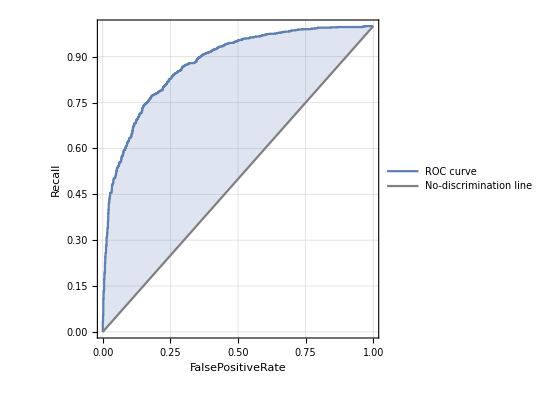
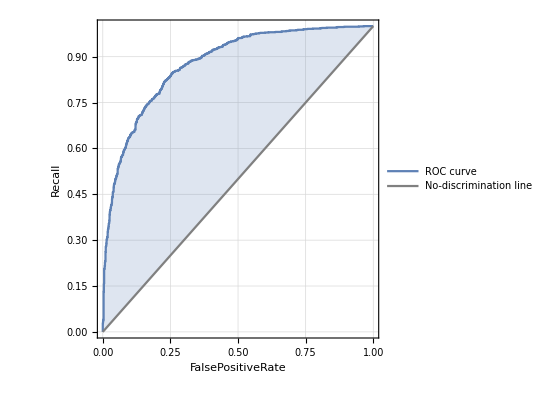
0.79
<|negative→0.771028,positive→0.811828|>
<|negative→0.825,positive→0.755|>
<|negative→-Graphics-,positive→-Graphics-|>
 |  |  |  |

```mathematica
cmNN/@{"Accuracy","Precision","Recall", "ROCCurve"}//TableForm
```

```mathematica
sentimentAnalysisLR=Classify[trainingDr2->labelReviewTraining,Method->"LogisticRegression"];
```

```mathematica
cmLR=ClassifierMeasurements[sentimentAnalysisLR,testingDr2->labelTraining];
```

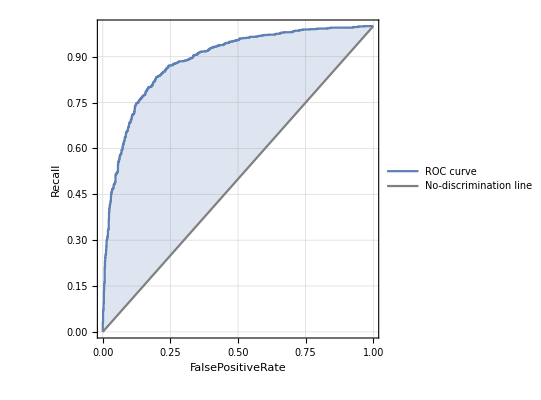
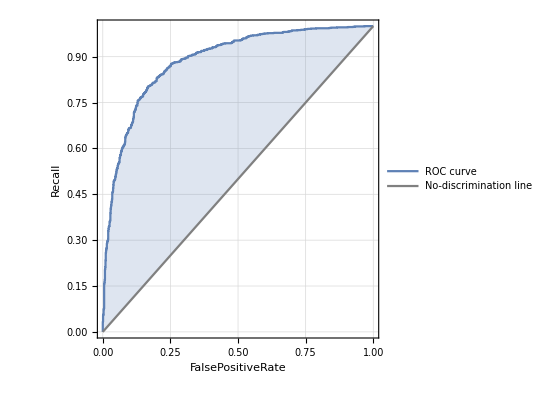
0.8115
<|negative→0.814965,positive→0.808111|>
<|negative→0.806,positive→0.817|>
<|negative→-Graphics-,positive→-Graphics-|>
 |  |  |  |

```mathematica
cmLR/@{"Accuracy","Precision","Recall", "ROCCurve"}//TableForm
```